```mathematica
list = Table[0, {30}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
list[[15]] = 1;
```

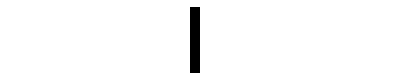

```mathematica
ArrayPlot[{list}]
```

```mathematica
rules = {
{0,0,0} -> 0,
{0,0,1} -> 1,
{0,1,0} -> 1,
{0,1,1} -> 1,
{1,0,0} -> 0,
{1,0,1} -> 1,
{1,1,0} -> 1,
{1,1,1} -> 0
}
```

{{0,0,0}→0,{0,0,1}→1,{0,1,0}→1,{0,1,1}→1,{1,0,0}→0,{1,0,1}→1,{1,1,0}→1,{1,1,1}→0}

```mathematica
Partition[list, 3,1] /. rules
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

(Note to myself : Here there are only 28 numbers because partition to three can only take the three outermost numbers to use. It can use the first and last number only with one three - partitions. The first rule has already been applied.)

```mathematica
Join[{0}, %, {0}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
step[seq_] := Join[{0}, Partition[seq, 3,1] /. rules, {0}]
```

```mathematica
(Note: step[seq_] is a function we have created to ourselves)
```

```mathematica
step[step[list]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Nest[step, list, 30]
```

{0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
matrix =NestList[step, list, 30]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,1,0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,1,1,0,0,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,0,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,1,1,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,1,0,0,1,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,1,1,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,1,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,0,0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot [%]
```

-Graphics-

```mathematica
Flatten[matrix]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,1,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
You can call a function, etc. by its number with %number (etc. [%21]). (Just remember to stop the kernel first so that it will update the input and output numbers to the code.) You can also name the functions (check previous "matrix").
```

```mathematica
rules1 = {0 -> {1,0}, 1 -> {0,1}}
```

{0→{1,0},1→{0,1}}

```mathematica
pattern = matrix /. rules1
```

{{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{1,0},{0,1},{0,1},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{1,0},{1,0},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{0,1},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{0,1},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{0,1},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{0,1},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{0,1},{0,1},{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}}

```mathematica
pattern1 = Accumulate[pattern]
```

{{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}},{{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{1,1},{0,2},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0},{2,0}},{{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{2,1},{1,2},{0,3},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0},{3,0}},{{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{3,1},{2,2},{2,2},{0,4},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0},{4,0}},{{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{4,1},{3,2},{2,3},{2,3},{0,5},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0},{5,0}},{{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{5,1},{4,2},{4,2},{3,3},{3,3},{0,6},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0},{6,0}},{{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{6,1},{5,2},{4,3},{5,2},{4,3},{3,4},{0,7},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0},{7,0}},{{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{7,1},{6,2},{6,2},{4,4},{6,2},{4,4},{3,5},{0,8},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0},{8,0}},{{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{8,1},{7,2},{6,3},{6,3},{4,5},{6,3},{4,5},{4,5},{0,9},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0},{9,0}},{{10,0},{10,0},{10,0},{10,0},{10,0},{9,1},{8,2},{8,2},{7,3},{7,3},{5,5},{7,3},{4,6},{4,6},{0,10},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0},{10,0}},{{11,0},{11,0},{11,0},{11,0},{10,1},{9,2},{8,3},{9,2},{8,3},{8,3},{6,5},{7,4},{4,7},{5,6},{0,11},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0},{11,0}},{{12,0},{12,0},{12,0},{11,1},{10,2},{10,2},{8,4},{10,2},{9,3},{9,3},{6,6},{7,5},{4,8},{5,7},{0,12},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0},{12,0}},{{13,0},{13,0},{12,1},{11,2},{10,3},{10,3},{8,5},{11,2},{10,3},{9,4},{6,7},{8,5},{5,8},{6,7},{0,13},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0},{13,0}},{{14,0},{13,1},{12,2},{12,2},{11,3},{11,3},{8,6},{12,2},{10,4},{9,5},{6,8},{9,5},{6,8},{6,8},{0,14},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0},{14,0}},{{15,0},{13,2},{12,3},{13,2},{12,3},{11,4},{8,7},{12,3},{10,5},{10,5},{6,9},{10,5},{6,9},{6,9},{0,15},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0},{15,0}},{{16,0},{13,3},{12,4},{14,2},{12,4},{11,5},{9,7},{13,3},{10,6},{10,6},{6,10},{10,6},{6,10},{7,9},{0,16},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0},{16,0}},{{17,0},{13,4},{12,5},{14,3},{12,5},{11,6},{10,7},{13,4},{10,7},{11,6},{7,10},{11,6},{6,11},{7,10},{0,17},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0},{17,0}},{{18,0},{13,5},{13,5},{15,3},{13,5},{11,7},{10,8},{13,5},{10,8},{12,6},{8,10},{11,7},{6,12},{8,10},{0,18},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0},{18,0}},{{19,0},{13,6},{14,5},{16,3},{13,6},{11,8},{11,8},{14,5},{10,9},{13,6},{8,11},{11,8},{6,13},{8,11},{0,19},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0},{19,0}},{{20,0},{13,7},{15,5},{16,4},{13,7},{11,9},{12,8},{14,6},{10,10},{13,7},{8,12},{12,8},{7,13},{9,11},{0,20},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0},{20,0}},{{21,0},{13,8},{15,6},{16,5},{14,7},{11,10},{12,9},{14,7},{11,10},{14,7},{8,13},{13,8},{8,13},{9,12},{0,21},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0},{21,0}},{{22,0},{13,9},{16,6},{16,6},{14,8},{11,11},{13,9},{14,8},{12,10},{14,8},{8,14},{14,8},{8,14},{9,13},{0,22},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0},{22,0}},{{23,0},{13,10},{16,7},{16,7},{15,8},{11,12},{13,10},{14,9},{12,11},{14,9},{8,15},{14,9},{8,15},{10,13},{0,23},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0},{23,0}},{{24,0},{13,11},{17,7},{16,8},{15,9},{11,13},{14,10},{15,9},{13,11},{15,9},{9,15},{15,9},{8,16},{10,14},{0,24},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0},{24,0}},{{25,0},{13,12},{17,8},{16,9},{16,9},{11,14},{15,10},{16,9},{14,11},{16,9},{10,15},{15,10},{8,17},{11,14},{0,25},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0},{25,0}},{{26,0},{13,13},{18,8},{16,10},{16,10},{11,15},{16,10},{17,9},{15,11},{17,9},{10,16},{15,11},{8,18},{11,15},{0,26},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0},{26,0}},{{27,0},{13,14},{18,9},{16,11},{17,10},{11,16},{17,10},{18,9},{16,11},{17,10},{10,17},{16,11},{9,18},{12,15},{0,27},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0},{27,0}},{{28,0},{13,15},{19,9},{16,12},{17,11},{11,17},{18,10},{19,9},{16,12},{17,11},{10,18},{17,11},{10,18},{12,16},{0,28},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0},{28,0}},{{29,0},{13,16},{19,10},{16,13},{18,11},{11,18},{19,10},{19,10},{16,13},{18,11},{10,19},{18,11},{10,19},{12,17},{0,29},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0},{29,0}},{{30,0},{13,17},{20,10},{16,14},{18,12},{11,19},{19,11},{19,11},{16,14},{18,12},{10,20},{18,12},{10,20},{13,17},{0,30},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0},{30,0}},{{31,0},{13,18},{20,11},{16,15},{19,12},{12,19},{20,11},{20,11},{17,14},{19,12},{11,20},{19,12},{10,21},{13,18},{0,31},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0},{31,0}}}

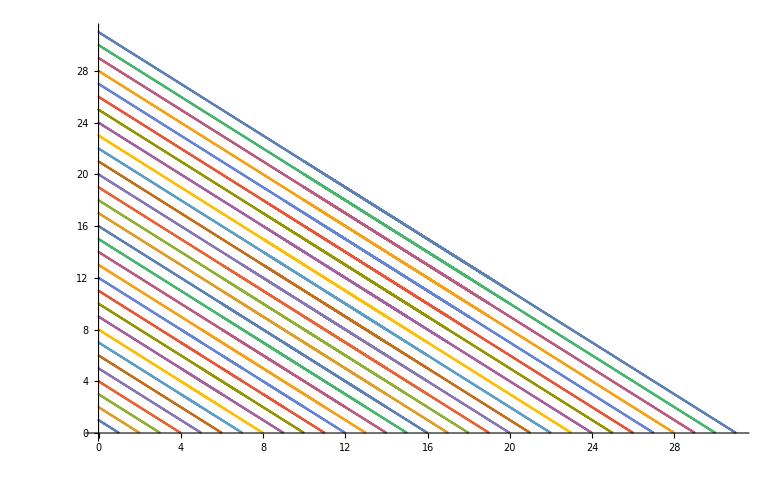

```mathematica
ListLinePlot[pattern1]
```

```mathematica
Maybe I still need to reset my rules for 0 and 1... XD
```